```mathematica
data:=Import["shootingdata.csv"][[2;;4939,3]]
Position[Counts[data],9]
```

{{Key[2018-01-06]},{Key[2018-02-01]},{Key[2018-04-01]},{Key[2018-06-29]},{Key[2019-01-28]}}

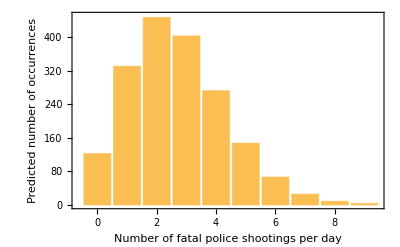

```mathematica
BarChart[{122.19,330.45,446.81,402.76,272.30,147.27,66.38,25.64,8.67,3.47},ChartLabels->{"0","1","2","3","4","5,","6","7","8","9 or more"},Frame->True,FrameLabel->{"Number of fatal police shootings per day","Predicted number of occurrences"},PlotRange->{0,450}]
```

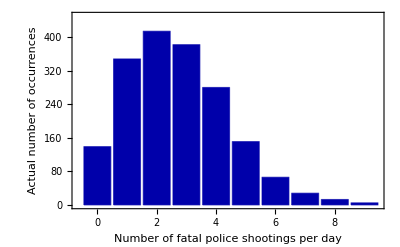

```mathematica
BarChart[{139,348,414,382,280,151,66,28,13,5},ChartLabels->{"0","1","2","3","4","5,","6","7","8","9 or more"},Frame->True,FrameLabel->{"Number of fatal police shootings per day","Actual number of occurrences"},PlotRange->{0,450},ChartStyle->Darker[Blue]]
```